```mathematica
Manipulate[
Module[{t,S,H,L,w,r1,r2,k,h,Tb,m,T,base,rectangular,annular,rplot},
t=0.0025;
S=0.01;
H:=n*S;

(*rectangle*)
L:=length/1000;
w:=width/1000;

(*annular*)
r1=0.003;
r2:=radius2/1000;


k=14;
h=35;
Tb=500;
m:=√((2*h)/(k*t));
T[x_]:=Tb*Cosh[m*(L-x)]/Cosh[m*L];

base:=5/1000;
rectangular:=Graphics3D[{
GrayLevel[0.5],Cuboid[{0,0,0},{base,w,H+S}],
RGBColor[0.08,0.51,1.],Table[Cuboid[{base,0,i*S},{base+L,w,i*S+t}],{i,1,n}]
}];

annular:=Graphics3D[{
GrayLevel[0.5],Cylinder[{{0,0,0},{0,0,H+S}},r1],
RGBColor[0.08,0.51,1.],Table[Cylinder[{{0,0,i*S},{0,0,i*S+t}},r2],{i,1,n}]
}];

rplot:=Plot3D[S+t+0.0001,{x,0,L},{y,0,w},Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[1,(T[x]-T[L])/(T[0]-T[L]),0]]];

Show[Switch[fin,1,rectangular,2,annular,3,Show[(*rectangular,*)rplot]],ViewPoint->{2,-2,1},Lighting->"Neutral",Boxed->False,ImageSize->{250,350}]

],
Control[{{fin,3,"fin type:"},{1->" rectangular ",2->" annular ",3->" rplot "},Setter}],
Control[{{n,3,"number of fins"},3,10,1,Appearance->"Labeled"}],
Style["fin measurements (mm)",Bold],
PaneSelector[{
1->Row[{
Control[{{length,10,"length"},5,20,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{width,20,"width"},20,50,1,Appearance->"Labeled",ImageSize->Small}]
}],
2->Control[{{radius2,10,"radius"},5,15,1,Appearance->"Labeled",ImageSize->Small}]
},Dynamic@fin]
]
```

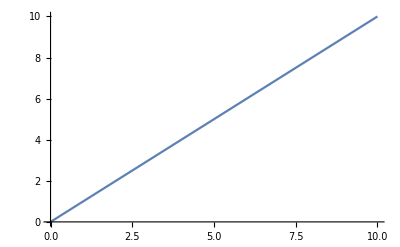

```mathematica
Plot[#&[x],{x,0,10}]
```

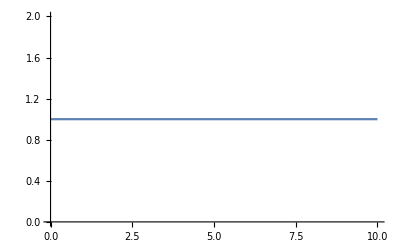

```mathematica
Plot[Normalize[x],{x,0,10}]
```

```mathematica
Module[{t,S,L,w,k,h,Tb,m,T,base,colfun,rplot},
t=0.0025;
S=0.01;
(*rectangle*)
L:=10/1000;
w:=20/1000;

k=14;
h=35;
Tb=500;
m:=√((2*h)/(k*t));
T[x_]:=Tb*Cosh[m*(L-x)]/Cosh[m*L];

base:=5/1000;

(*colfun:=Function[{x,y,z},RGBColor[1,Rescale[T[x],{T[L],Tb}],0]];*)
colfun:=Function[{x,y,z},RGBColor[1,z,0]];

(*rplot:=Plot3D[S+t,{x,0,L},{y,0,w},Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[1,(T[x]-T[L])/(T[0]-T[L]),0]]];*)

rplot:=Plot3D[(*S+t*)T[x],{x,0,L},{y,0,w},Mesh->None,ColorFunction->colfun];

Show[rplot,ViewPoint->{2,-2,1},Lighting->"Neutral",Boxed->False,ImageSize->400]

(*Maximize[T[x],x]*)
]
```

-Graphics3D-

```mathematica
Module[{f,xlim},
f[x_]:=10*x;
xlim=100;
Plot3D[0,{x,0,xlim},{y,0,1},Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[1,f[x]/f[1](*(f[x]-f[0])/(f[1]-f[0])*),0]]]
]
```

-Graphics3D-


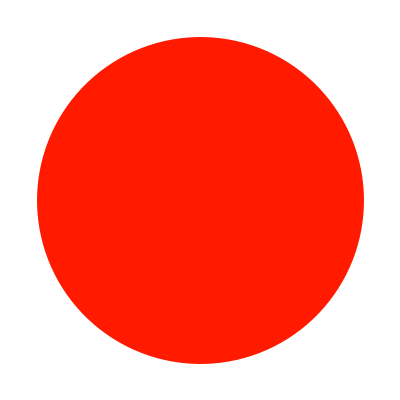
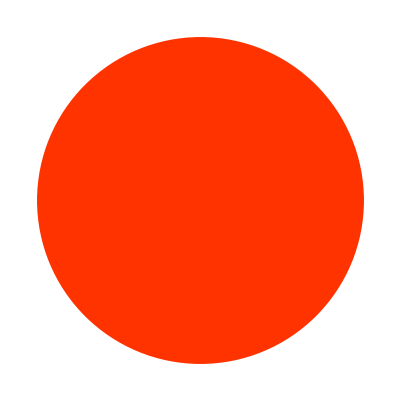
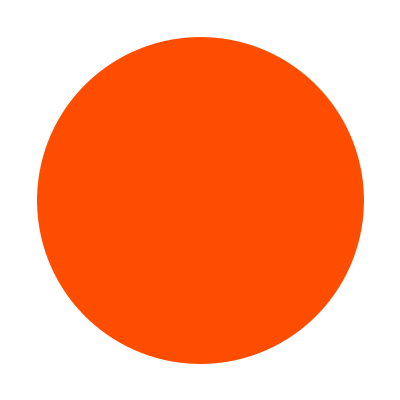
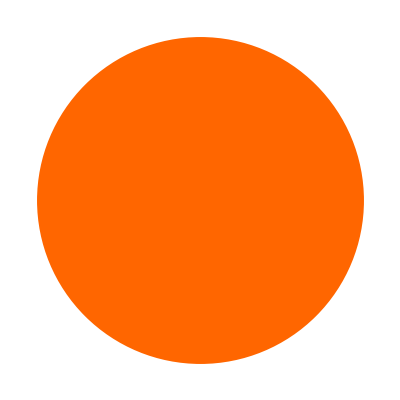
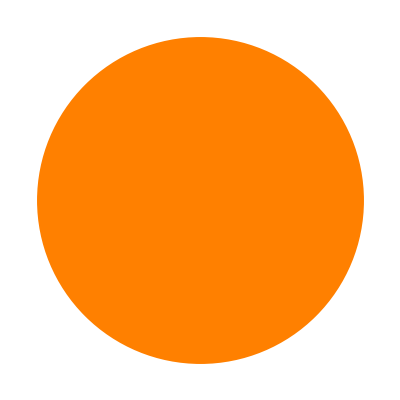
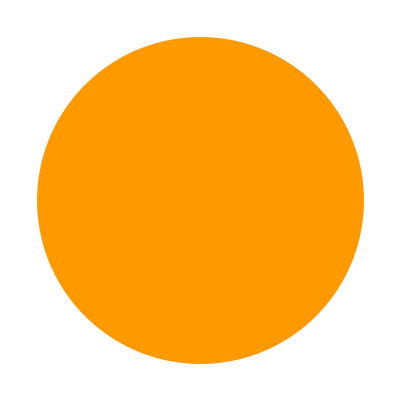
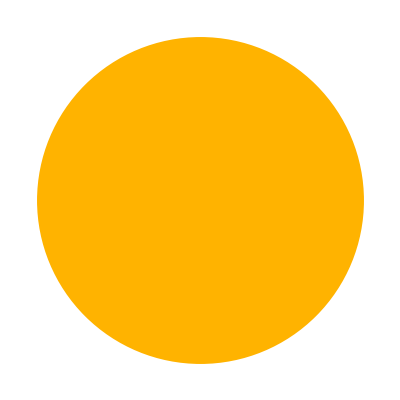
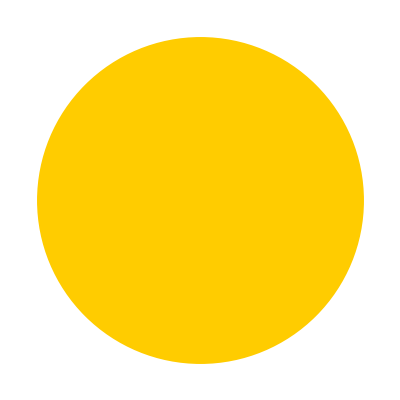

```mathematica
Table[Graphics[{RGBColor[1,i,0],Disk[]}],{i,0,1,0.1}]
```